=== [1/4] 挂载 MX 数据，剥离纯空间无向骨架 ===

[空间剥离完成] 当前瞬时空间节点数: 57291, 空间拓扑边数: 62318

=== [2/4] 启动 O(E) 极速 Forman-Ricci 曲率扫描 ===

正在计算全宇宙 8 万节点拓扑曲率 (预计数秒内完成)...

{5.99594,Null}

[曲率计算完成] 极端真空曲率(蓝): -5., 极端奇点曲率(红): 3., 背景平均曲率: 0.9

=== [3/4] 绘制全局：曲率态密度直方图 ===

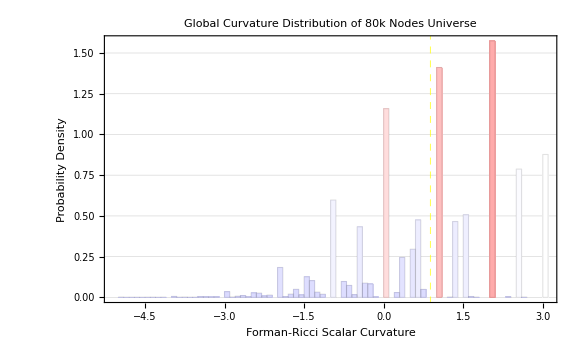

=== [4/4] 自动切取超大核心进行渲染 ===

正在定位最强源 (节点 ID: 76)... 正在切取局部 1500 节点...

正在进行背景独立引力色图渲染...

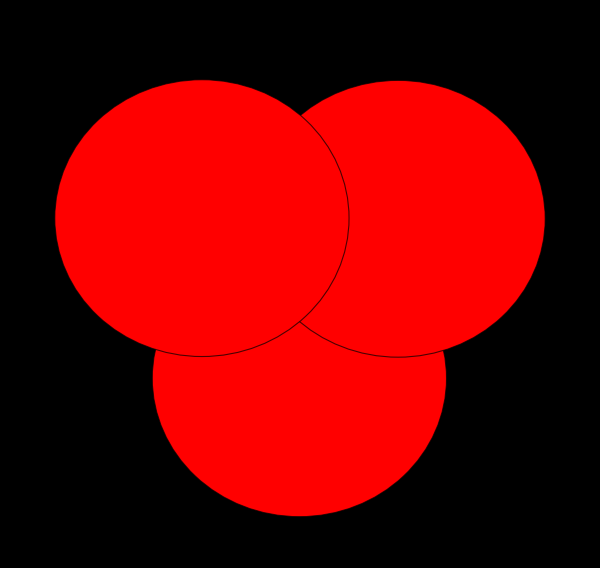

[结束]！

```mathematica
<<"C:\\Users\\王鑫\\Desktop\\maxwell_dis_par_100_win100_and_400_win70.mx"
$HistoryLength=0;
ClearSystemCache[];

Print[Style["=== [1/4] 挂载 MX 数据，剥离纯空间无向骨架 ===",Blue,Bold,14]];


If[!ValueQ[universe],Print[Style["[错误] 未检测到 universe 变量！请先导入你的 .mx 文件。",Red,Bold]];
Abort[]];

(*剥离时间因果，只保留瞬时空间叶片 (无向边)*)
activeEdges=Cases[EdgeList[universe],_UndirectedEdge];
spaceGraph=Graph[activeEdges];
vList=VertexList[spaceGraph];
vCount=Length[vList];
eCount=Length[activeEdges];

Print[StringForm["[空间剥离完成] 当前瞬时空间节点数: ``, 空间拓扑边数: ``",vCount,eCount]];

(* =========================================================================*)
Print[Style["\n=== [2/4] 启动 O(E) 极速 Forman-Ricci 曲率扫描 ===",Blue,Bold,14]];

(*预计算度数，提速查询*)
degRules=AssociationThread[vList,VertexDegree[spaceGraph]];
edgeCurvatures=Association[];

(*记录节点曲率的累加器，防止 $O(N*E)$ 遍历导致死机，采用 $O(E)$ 极速累加*)
nodeCurvSum=AssociationMap[0.0&,vList];
nodeCurvCount=AssociationMap[0.0&,vList];

Print["正在计算全宇宙 8 万节点拓扑曲率 (预计数秒内完成)..."];

AbsoluteTiming[Monitor[Do[e=activeEdges[[i]];
u=e[[1]];v=e[[2]];
du=degRules[u];
dv=degRules[v];
(*寻找共享该边的三角形数量 (高度凝聚的拓扑疤痕核心特征)*)triangles=Length[Intersection[AdjacencyList[spaceGraph,u],AdjacencyList[spaceGraph,v]]];
(*Forman-Ricci 曲率离散方程*)curv=4-du-dv+3*triangles;
(*累加到两端节点*)nodeCurvSum[u]+=curv;
nodeCurvSum[v]+=curv;
nodeCurvCount[u]+=1.0;
nodeCurvCount[v]+=1.0;,{i,1,eCount}],Row[{"已扫描边数: ",i,"/",eCount}]];
(*求平均标量曲率*)nodeCurvatures=AssociationMap[If[nodeCurvCount[#]>0,nodeCurvSum[#]/nodeCurvCount[#],0.0]&,vList];]

curvVals=Values[nodeCurvatures];
minC=Min[curvVals];
maxC=Max[curvVals];
meanC=Mean[curvVals];

Print[StringForm["[曲率计算完成] 极端真空曲率(蓝): ``, 极端奇点曲率(红): ``, 背景平均曲率: ``",Round[minC,0.1],Round[maxC,0.1],Round[meanC,0.1]]];

(* =========================================================================*)
Print[Style["\n=== [3/4] 绘制全局：曲率态密度直方图 ===",Purple,Bold,14]];


curvatureHistogram=Histogram[curvVals,100,"PDF",PlotTheme->"Detailed",Frame->True,FrameLabel->{Style["Forman-Ricci Scalar Curvature",12,Bold],Style["Probability Density",12,Bold]},PlotLabel->Style["Global Curvature Distribution of 80k Nodes Universe",13,Bold],ColorFunction->(Blend[{{minC,Blue},{meanC,White},{maxC,Red}},#1]&),ColorFunctionScaling->False,GridLines->{{meanC},Automatic},GridLinesStyle->Directive[Yellow,Dashed],ImageSize->580];
Print[curvatureHistogram];

(* =========================================================================*)
Print[Style["\n=== [4/4] 自动切取超大核心进行渲染 ===",Purple,Bold,14]];


maxGravityNode=MaximalBy[vList,nodeCurvatures[#]&,1][[1]];

Print[StringForm["正在定位最强源 (节点 ID: ``)... 正在切取局部 1500 节点...",maxGravityNode]];

(*BFS 广度优先搜索切取局部 1500 节点流形，防止渲染 8 万节点导致显卡崩溃*)
visited={maxGravityNode};
queue={maxGravityNode};

While[Length[visited]<1500&&Length[queue]>0,currNode=First[queue];
queue=Rest[queue];
neighbors=AdjacencyList[spaceGraph,currNode];
unvisited=Complement[neighbors,visited];
visited=Join[visited,unvisited];
queue=Join[queue,unvisited];];

localNodes=Take[visited,Min[1500,Length[visited]]];
localPatch=Subgraph[spaceGraph,localNodes];

(*定义引力色标：蓝色(负)->膨胀真空；白色(零)->平坦空间；红色(正)->引力汇聚区*)
CurvatureColor[c_]:=Blend[{{minC,Blue},{meanC,White},{maxC,Red}},c];

Print["正在进行背景独立引力色图渲染..."];
ricciGraphPlot=Graph[localPatch,VertexSize->1.5,VertexStyle->{v_:>CurvatureColor[nodeCurvatures[v]]},EdgeStyle->Directive[GrayLevel[0.8],Opacity[0.15]],GraphLayout->"SpringElectricalEmbedding",PlotLabel->Style["Local Galaxy Core: Emergent Ricci Curvature\n(Red: Gravity Well | Blue: Cosmic Voids)",13,Bold],ImageSize->600,Background->Black];
Print[ricciGraphPlot];

Print[Style["\n[结束]！",Darker[Green],Bold,14]];
```

=== [1/4] 提取实验靶点 ===

奇点 ID: 80796 (曲率: 3.) | 深度真空 ID: 18759 (曲率: -5.)

视界轨道 ID: 37692 (曲率: 3.)

=== [2/4] 构建大尺度离散时空演化算符 ===

[就绪] 8万阶稀疏演化算符已生成，准备发射波包...

=== [3/4] 实验 A (Trapping) ===

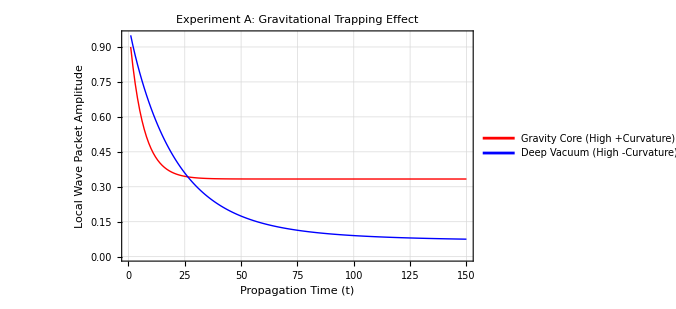

=== [4/4] 实验 B (Attraction) ===

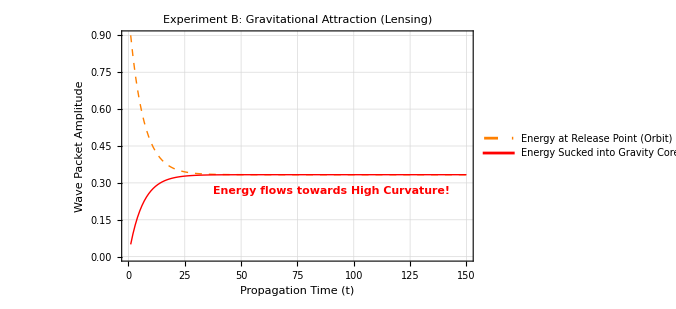

测试完成！

```mathematica
Print[Style["=== [1/4] 提取实验靶点 ===",Blue,Bold,14]];

(*确保数据存在*)
If[!ValueQ[spaceGraph]||!ValueQ[nodeCurvatures],Print[Style["[错误] 内存中丢失 spaceGraph 或曲率数据！请先运行上一个计算曲率的代码。",Red,Bold]];
Abort[]];

vList=VertexList[spaceGraph];
vCount=Length[vList];

(*安全获取节点：使用 SortBy 彻底杜绝空集报错*)
sortedNodes=SortBy[vList,nodeCurvatures[#]&];
coreNode=Last[sortedNodes];  (*曲率最高：引力奇点*)
vacNode=First[sortedNodes];  (*曲率最低：深度真空*)


coreNeighbors=AdjacencyList[spaceGraph,coreNode];
orbitCandidates=Complement[coreNeighbors,{coreNode}];
If[Length[orbitCandidates]==0,orbitCandidates=Complement[vList,{coreNode}]];


orbitNode=First[SortBy[orbitCandidates,nodeCurvatures[#]&]];

coreIdx=VertexIndex[spaceGraph,coreNode];
vacIdx=VertexIndex[spaceGraph,vacNode];
orbitIdx=VertexIndex[spaceGraph,orbitNode];

Print[StringForm["奇点 ID: `` (曲率: ``) | 深度真空 ID: `` (曲率: ``)",coreNode,Round[nodeCurvatures[coreNode],0.1],vacNode,Round[nodeCurvatures[vacNode],0.1]]];
Print[StringForm["视界轨道 ID: `` (曲率: ``)",orbitNode,Round[nodeCurvatures[orbitNode],0.1]]];

(* =========================================================================*)
Print[Style["\n=== [2/4] 构建大尺度离散时空演化算符 ===",Blue,Bold,14]];

(*构建演化矩阵:P=I-alpha*L (扩散/波包演化)*)
lapMat=N[KirchhoffMatrix[spaceGraph]];
alpha=0.05; (*安全演化步长*)
propOp=IdentityMatrix[vCount,SparseArray]-alpha*lapMat;

Print["[就绪] 8万阶稀疏演化算符已生成，准备发射波包..."];

(* =========================================================================*)
Print[Style["\n=== [3/4] 实验 A (Trapping) ===",Purple,Bold,14]];

steps=150;


stateCore=SparseArray[{coreIdx->1.0},vCount];
coreDecay=Table[stateCore=propOp.stateCore;
stateCore[[coreIdx]],{t,1,steps}];


stateVac=SparseArray[{vacIdx->1.0},vCount];
vacDecay=Table[stateVac=propOp.stateVac;
stateVac[[vacIdx]],{t,1,steps}];

plotTrapping=ListLinePlot[{coreDecay,vacDecay},PlotStyle->{Directive[Thick,Red],Directive[Thick,Blue]},PlotLegends->Placed[{"Gravity Core (High +Curvature)","Deep Vacuum (High -Curvature)"},Top],PlotTheme->"Detailed",Frame->True,FrameLabel->{Style["Propagation Time (t)",12,Bold],Style["Local Wave Packet Amplitude",12,Bold]},PlotLabel->Style["Experiment A: Gravitational Trapping Effect",13,Bold],GridLines->Automatic,PlotRange->All,ImageSize->500];
Print[plotTrapping];

(* =========================================================================*)
Print[Style["\n=== [4/4] 实验 B (Attraction) ===",Purple,Bold,14]];

(*在“事件视界轨道”释放能量波包*)
stateOrbit=SparseArray[{orbitIdx->1.0},vCount];
orbitToCoreFlow=Table[0.0,{steps}];
orbitLocalDecay=Table[0.0,{steps}];

Do[stateOrbit=propOp.stateOrbit;
orbitLocalDecay[[t]]=stateOrbit[[orbitIdx]];
orbitToCoreFlow[[t]]=stateOrbit[[coreIdx]]; ,{t,1,steps}];

plotAttraction=ListLinePlot[{orbitLocalDecay,orbitToCoreFlow},PlotStyle->{Directive[Thick,Orange,Dashed],Directive[Thick,Red]},PlotLegends->Placed[{"Energy at Release Point (Orbit)","Energy Sucked into Gravity Core"},Top],PlotTheme->"Detailed",Frame->True,FrameLabel->{Style["Propagation Time (t)",12,Bold],Style["Wave Packet Amplitude",12,Bold]},PlotLabel->Style["Experiment B: Gravitational Attraction (Lensing)",13,Bold],GridLines->Automatic,PlotRange->All,Epilog->{Text[Style["Energy flows towards High Curvature!",Red,Bold,11],{steps*0.6,Max[orbitToCoreFlow]*0.8}]},ImageSize->500];
Print[plotAttraction];

Print[Style["\n 测试完成！",Darker[Green],Bold,14]];
```